```mathematica
lor=d/(     ((x-a)/b)^2  + 1    ) + c;


ga=b*Exp[-(-a+x)^2  /(2 *s^2)] +c;
```

```mathematica
FindFit[a10, -(v*g (-a+x))/(π (g^2/4+(-a+x)^2)^2),{{a,-3200},{v,-3000},{g,150}},x]




a1ten=NonlinearModelFit[a10, { -(v*g (-a+x))/(π (g^2/4+(-a+x)^2)^2),150<g<160, -1500<v<-300, -3200<a<-3000},{a,v,g } ,x ]
```

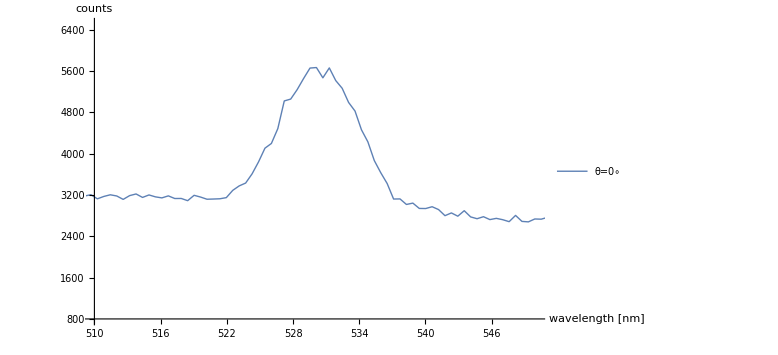

```mathematica
azer=Import["C:\\Users\\Peggy\\Desktop\\raman spectroscopz\\Raman Spectroscopy\\ramanSpectroscopy5\\analzyer angle\\SI_100_Ang_220_0000.csv","Table"];
a0=Take[azer, {290,410}];
aa0=ListLinePlot[a0, LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[0.01]] ,   AxesLabel->{" wavelength [nm]", " counts"}  ,PlotStyle->Directive[Thickness[Tiny],"LineColor"->Lighter[Red],AbsoluteThickness[1]],PlotLegends->LineLegend[{"θ=0∘"}], PlotRange->{{510,550}, {800,6500}}]
```

```mathematica
NonlinearModelFit[a0, { d/(     ((x-a)/b)^2  + 1    ) + c},{a,b,c,d} ,x]
```

FittedModel[1703.72+(3.71084×10^7)/(1+6.81395×10^-15 (-1.84585×10^9+x)^2)]

```mathematica
%30["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 1.84585×10^9 | 1.18346×10^11 | 0.015597 | 0.987582
b | 1.21144×10^7 | 1.20211×10^13 | 1.00775×10^-6 | 0.999999
c | 1703.72 | 3.25663×10^9 | 5.23153×10^-7 | 1.
d | 3.71084×10^7 | 1.96237×10^12 | 0.00001891 | 0.999985

```mathematica
%30["AdjustedRSquared"]
```

0.945741

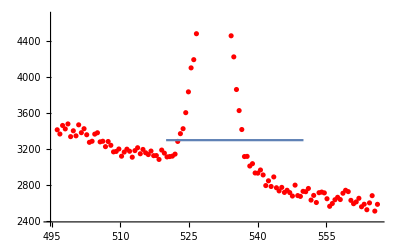

```mathematica
Show[ListPlot[a0,PlotStyle->Red],Plot[1703.71975168415+(3.7108428776851185*^7)/(1+6.813953055796133*^-15 (-1.8458468881695695*^9+x)^2),{x,520,550}]]
```

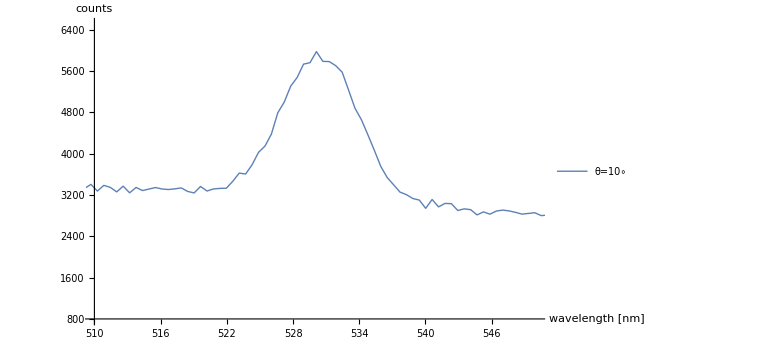

```mathematica
a10=Import["C:\\Users\\Peggy\\Desktop\\raman spectroscopz\\Raman Spectroscopy\\ramanSpectroscopy5\\analzyer angle\\SI_100_Ang_220_0010.csv","Table"];
a10=Take[a0, {200,585}];
aa10=ListLinePlot[a10, LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[0.01]] ,  AxesLabel->{" wavelength [nm]", " counts"}  ,PlotStyle->Directive[Thickness[Medium],"LineColor"->Lighter[Blue],AbsoluteThickness[1]],PlotLegends->LineLegend[{"θ=10∘"},LegendLayout->table], PlotRange->{{510,550}, {800,6500}}]
```

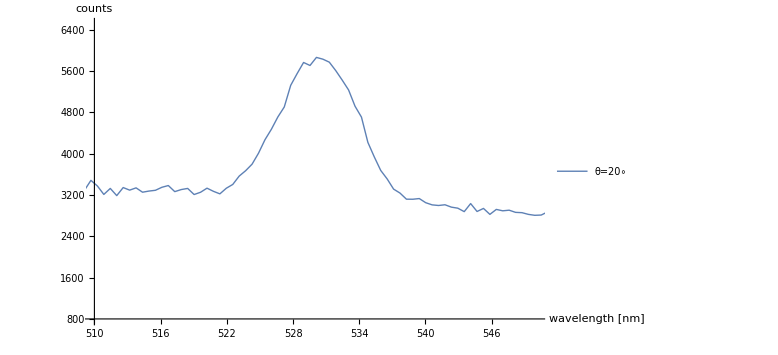

```mathematica
a20=Import["C:\\Users\\Peggy\\Desktop\\raman spectroscopz\\Raman Spectroscopy\\ramanSpectroscopy5\\analzyer angle\\SI_100_Ang_220_0020.csv","Table"];
a10=Take[a0, {200,585}];
aa20=ListLinePlot[a20, LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[0.01]] , AxesLabel->{" wavelength [nm]", " counts"}  ,PlotStyle->Directive[Thickness[Tiny],"LineColor"->Lighter[Green],AbsoluteThickness[1]],PlotLegends->LineLegend[{"θ=20∘"},LegendLayout->table], PlotRange->{{510,550}, {800,6500}}]
```

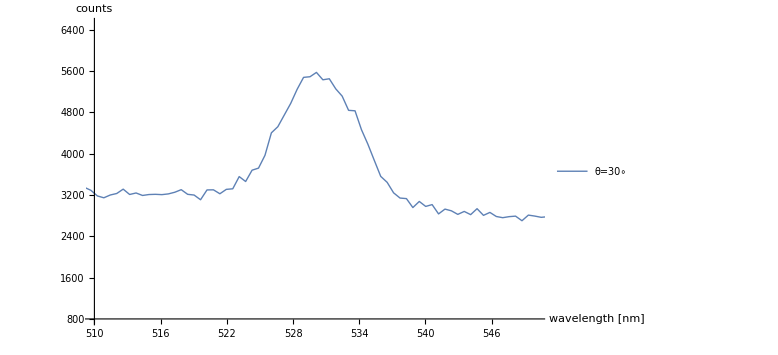

```mathematica
a30=Import["C:\\Users\\Peggy\\Desktop\\raman spectroscopz\\Raman Spectroscopy\\ramanSpectroscopy5\\analzyer angle\\SI_100_Ang_220_0030.csv","Table"];
a10=Take[a0, {200,585}];
aa30=ListLinePlot[a30, LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[0.01]] ,  AxesLabel->{" wavelength [nm]", " counts"}  ,PlotStyle->Directive[Thickness[Tiny],"LineColor"->Lighter[Orange],AbsoluteThickness[1]],PlotLegends->LineLegend[{"θ=30∘"},LegendLayout->table], PlotRange->{{510,550}, {800,6500}}]
```

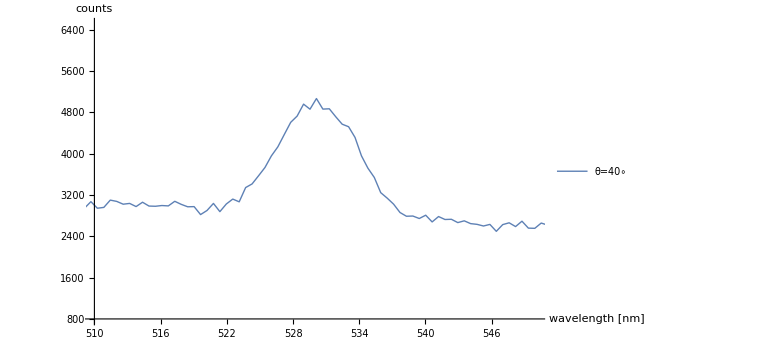

```mathematica
a40=Import["C:\\Users\\Peggy\\Desktop\\raman spectroscopz\\Raman Spectroscopy\\ramanSpectroscopy5\\analzyer angle\\SI_100_Ang_220_0040.csv","Table"];
a10=Take[a0, {200,585}];
aa40=ListLinePlot[a40, LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[0.01]] , AxesLabel->{" wavelength [nm]", " counts"} ,PlotStyle->Directive[Thickness[Tiny],"LineColor"->Lighter[Pink],AbsoluteThickness[1]],PlotLegends->LineLegend[{"θ=40∘"},LegendLayout->table], PlotRange->{{510,550}, {800,6500}}]
```

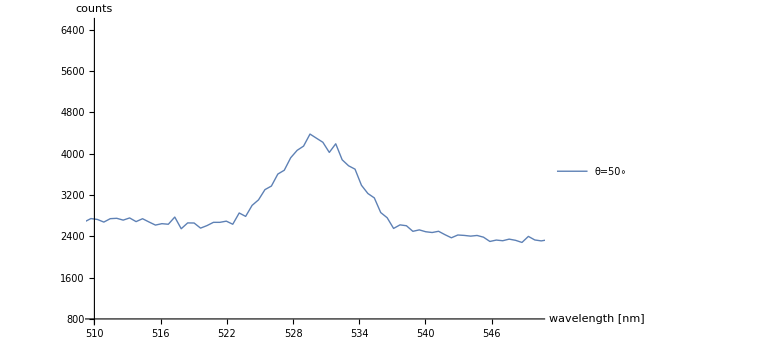

```mathematica
a50=Import["C:\\Users\\Peggy\\Desktop\\raman spectroscopz\\Raman Spectroscopy\\ramanSpectroscopy5\\analzyer angle\\SI_100_Ang_220_0050.csv","Table"];
a10=Take[a0, {200,585}];
aa50=ListLinePlot[a50, LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[0.01]] , AxesLabel->{" wavelength [nm]", " counts"}  ,PlotStyle->Directive[Thickness[Tiny],"LineColor"->Lighter[Gray],AbsoluteThickness[1]],PlotLegends->LineLegend[{"θ=50∘"},LegendLayout->table], PlotRange->{{510,550}, {800,6500}}]
```

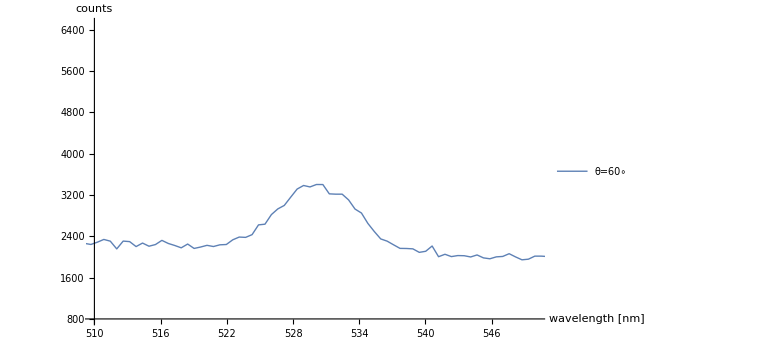

```mathematica
a60=Import["C:\\Users\\Peggy\\Desktop\\raman spectroscopz\\Raman Spectroscopy\\ramanSpectroscopy5\\analzyer angle\\SI_100_Ang_220_0060.csv","Table"];
a10=Take[a0, {200,585}];
aa60=ListLinePlot[a60, LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[0.01]] , AxesLabel->{" wavelength [nm]", " counts"}  ,PlotStyle->Directive[Thickness[Tiny],"LineColor"->Lighter[Cyan],AbsoluteThickness[1]],PlotLegends->LineLegend[{"θ=60∘"},LegendLayout->table], PlotRange->{{510,550}, {800,6500}}]
```

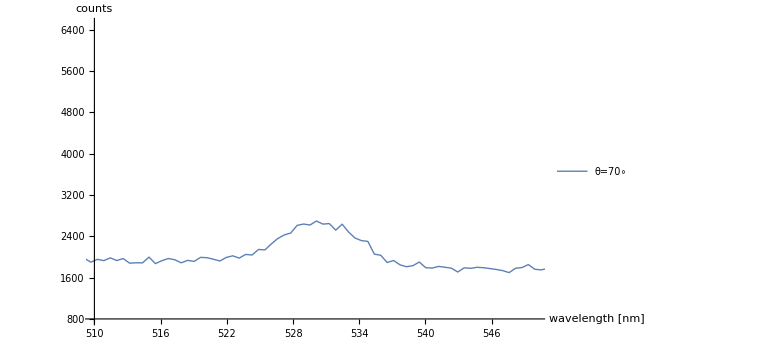

```mathematica
a70=Import["C:\\Users\\Peggy\\Desktop\\raman spectroscopz\\Raman Spectroscopy\\ramanSpectroscopy5\\analzyer angle\\SI_100_Ang_220_0070.csv","Table"];
a10=Take[a0, {200,585}];
aa70=ListLinePlot[a70, LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[0.01]] , AxesLabel->{" wavelength [nm]", " counts"}  ,PlotStyle->Directive[Thickness[Tiny],"LineColor"-> Lighter[Purple],AbsoluteThickness[1]],PlotLegends->LineLegend[{"θ=70∘"},LegendLayout->table], PlotRange->{{510,550}, {800,6500}}]
```

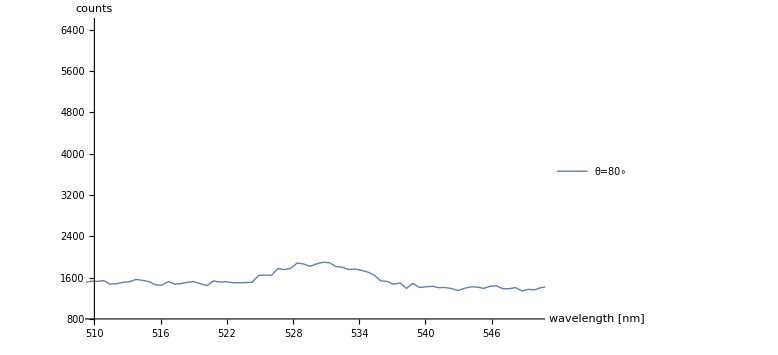

```mathematica
a80=Import["C:\\Users\\Peggy\\Desktop\\raman spectroscopz\\Raman Spectroscopy\\ramanSpectroscopy5\\analzyer angle\\SI_100_Ang_220_0080.csv","Table"];
a10=Take[a0, {200,585}];
aa80=ListLinePlot[a80, LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[0.01]] , AxesLabel->{" wavelength [nm]", " counts"}  ,PlotStyle->Directive[Thickness[Tiny],"LineColor"->Lighter[Brown ],AbsoluteThickness[1]],PlotLegends->LineLegend[{"θ=80∘"},LegendLayout->table], PlotRange->{{510,550}, {800,6500}}]
```

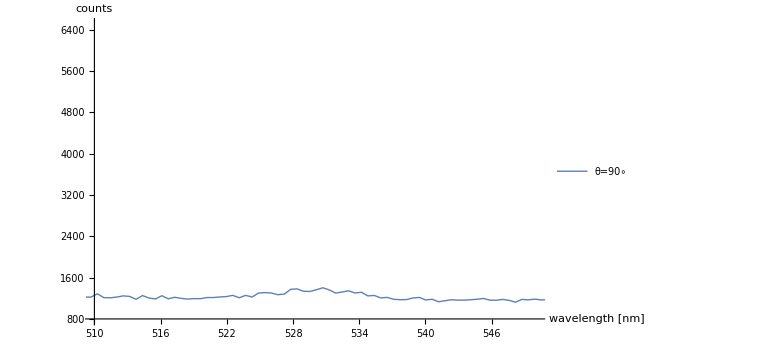

```mathematica
a90=Import["C:\\Users\\Peggy\\Desktop\\raman spectroscopz\\Raman Spectroscopy\\ramanSpectroscopy5\\analzyer angle\\SI_100_Ang_220_0090.csv","Table"];
a10=Take[a0, {200,585}];
aa90=ListLinePlot[a90, LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[0.01]] , AxesLabel->{" wavelength [nm]", " counts"}  ,PlotStyle->Directive[Thickness[Tiny],"LineColor"->Lighter[Magenta],AbsoluteThickness[1]],PlotLegends->LineLegend[{"θ=90∘"},LegendLayout->table], PlotRange->{{510,550}, {800,6500}}]
```

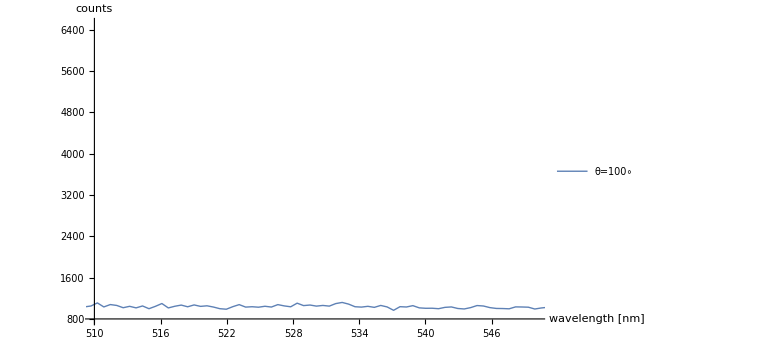

```mathematica
a100=Import["C:\\Users\\Peggy\\Desktop\\raman spectroscopz\\Raman Spectroscopy\\ramanSpectroscopy5\\analzyer angle\\SI_100_Ang_220_0100.csv","Table"];
a10=Take[a0, {200,585}];
aa100=ListLinePlot[a100, LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[0.01]] , AxesLabel->{" wavelength [nm]", " counts"}  ,PlotStyle->Directive[Thickness[Tiny],"LineColor"->Lighter[Yellow],AbsoluteThickness[1]],PlotLegends->LineLegend[{"θ=100∘"},LegendLayout->table], PlotRange->{{510,550}, {800,6500}}]
```

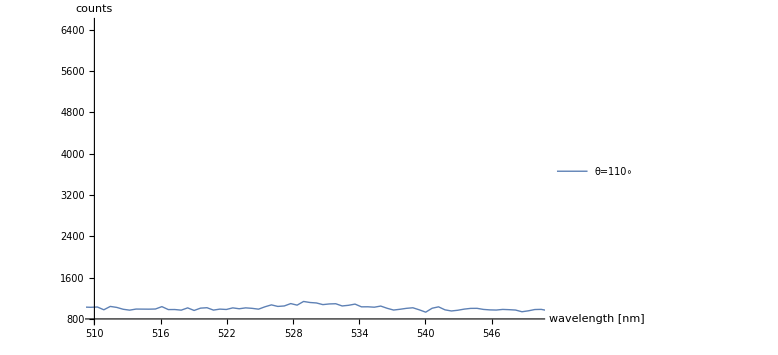

```mathematica
a110=Import["C:\\Users\\Peggy\\Desktop\\raman spectroscopz\\Raman Spectroscopy\\ramanSpectroscopy5\\analzyer angle\\SI_100_Ang_220_0110.csv","Table"];
a10=Take[a0, {200,585}];
aa110=ListLinePlot[a110, LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[0.01]] , AxesLabel->{" wavelength [nm]", " counts"}  ,PlotStyle->Directive[Thickness[Tiny],"LineColor"->Red,AbsoluteThickness[1]],PlotLegends->LineLegend[{"θ=110∘"},LegendLayout->table], PlotRange->{{510,550}, {800,6500}}]
```

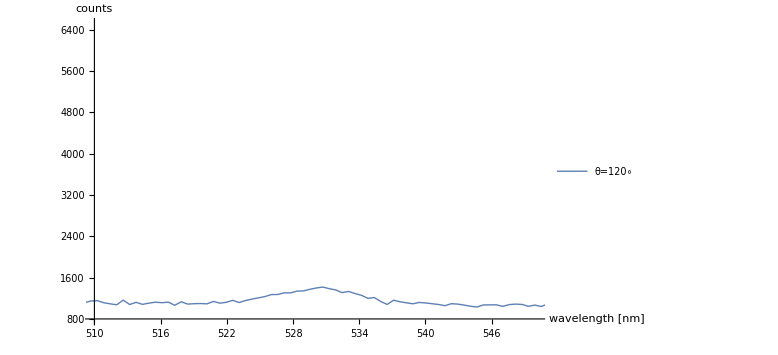

```mathematica
a120=Import["C:\\Users\\Peggy\\Desktop\\raman spectroscopz\\Raman Spectroscopy\\ramanSpectroscopy5\\analzyer angle\\SI_100_Ang_220_0120.csv","Table"];
a10=Take[a0, {200,585}];
aa120=ListLinePlot[a120, LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[0.01]] , AxesLabel->{" wavelength [nm]", " counts"}  ,PlotStyle->Directive[Thickness[Tiny],"LineColor"->Green,AbsoluteThickness[1]],PlotLegends->LineLegend[{"θ=120∘"},LegendLayout->table], PlotRange->{{510,550}, {800,6500}}]
```

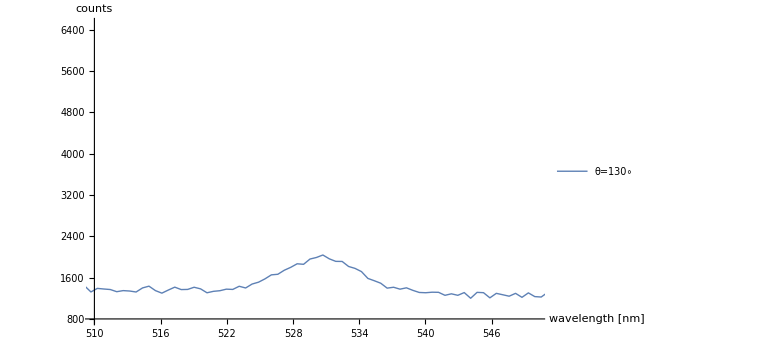

```mathematica
a130=Import["C:\\Users\\Peggy\\Desktop\\raman spectroscopz\\Raman Spectroscopy\\ramanSpectroscopy5\\analzyer angle\\SI_100_Ang_220_0130.csv","Table"];
a10=Take[a0, {200,585}];
aa130=ListLinePlot[a130, LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[0.01]] , AxesLabel->{" wavelength [nm]", " counts"}  ,PlotStyle->Directive[Thickness[Tiny],"LineColor"->Blue,AbsoluteThickness[1]],PlotLegends->LineLegend[{"θ=130∘"},LegendLayout->table], PlotRange->{{510,550}, {800,6500}}]
```

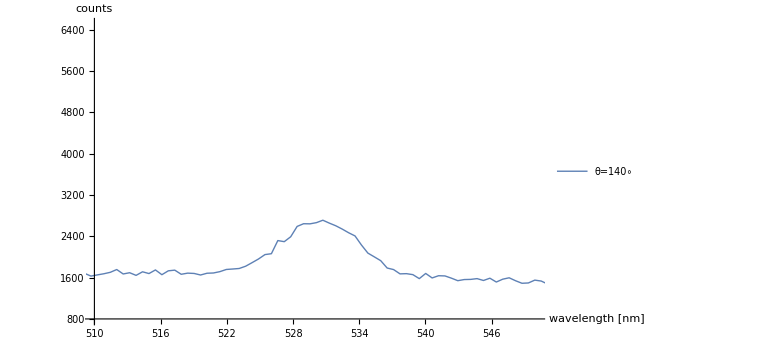

```mathematica
a140=Import["C:\\Users\\Peggy\\Desktop\\raman spectroscopz\\Raman Spectroscopy\\ramanSpectroscopy5\\analzyer angle\\SI_100_Ang_220_0140.csv","Table"];
a10=Take[a0, {200,585}];
aa140=ListLinePlot[a140, LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[0.01]] , AxesLabel->{" wavelength [nm]", " counts"}  ,PlotStyle->Directive[Thickness[Tiny],"LineColor"->Black,AbsoluteThickness[1]],PlotLegends->LineLegend[{"θ=140∘"},LegendLayout->table], PlotRange->{{510,550}, {800,6500}}]
```

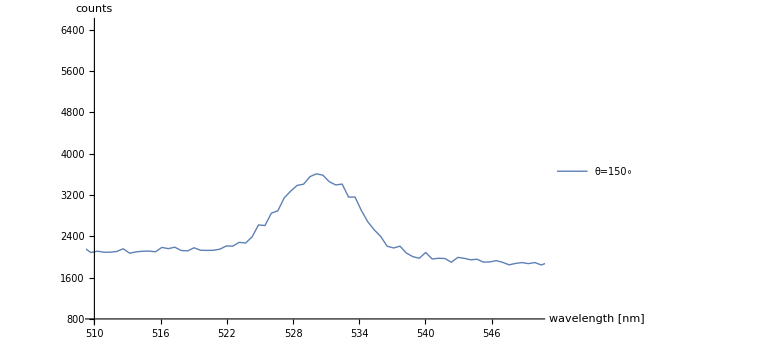

```mathematica
a150=Import["C:\\Users\\Peggy\\Desktop\\raman spectroscopz\\Raman Spectroscopy\\ramanSpectroscopy5\\analzyer angle\\SI_100_Ang_220_0150.csv","Table"];
a10=Take[a0, {200,585}];
aa150=ListLinePlot[a150, LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[0.01]] , AxesLabel->{" wavelength [nm]", " counts"}  ,PlotStyle->Directive[Thickness[Tiny],"LineColor"->Orange,AbsoluteThickness[1]],PlotLegends->LineLegend[{"θ=150∘"},LegendLayout->table], PlotRange->{{510,550}, {800,6500}}]
```

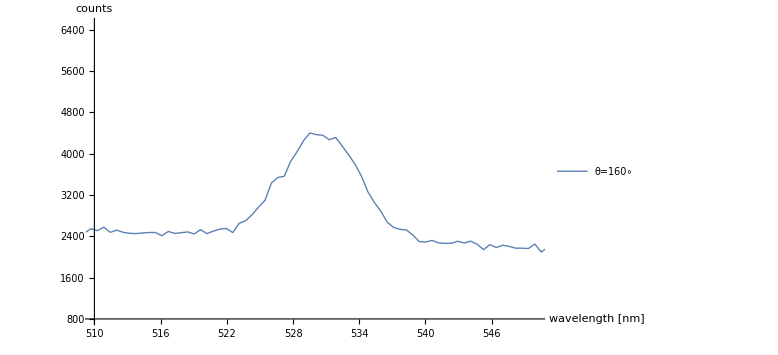

```mathematica
a160=Import["C:\\Users\\Peggy\\Desktop\\raman spectroscopz\\Raman Spectroscopy\\ramanSpectroscopy5\\analzyer angle\\SI_100_Ang_220_0160.csv","Table"];
a10=Take[a0, {200,585}];
aa160=ListLinePlot[a160, LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[0.01]] , AxesLabel->{" wavelength [nm]", " counts"}  ,PlotStyle->Directive[Thickness[Tiny],"LineColor"->Pink,AbsoluteThickness[1]],PlotLegends->LineLegend[{"θ=160∘"},LegendLayout->table], PlotRange->{{510,550}, {800,6500}}]
```

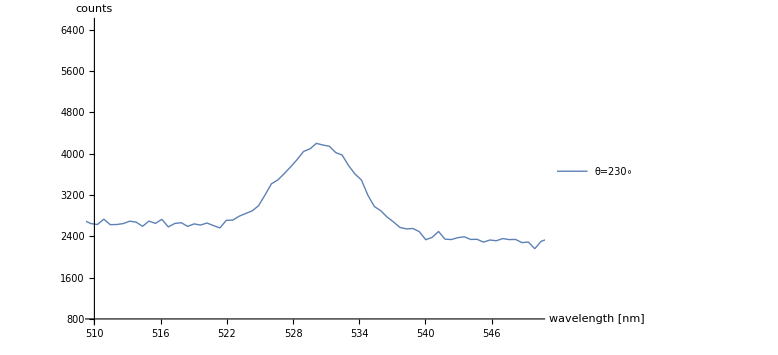

```mathematica
a230=Import["C:\\Users\\Peggy\\Desktop\\raman spectroscopz\\Raman Spectroscopy\\ramanSpectroscopy5\\analzyer angle\\SI_100_Ang_220_0230.csv","Table"];
a10=Take[a0, {200,585}];
aa230=ListLinePlot[a230, LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[0.01]] , AxesLabel->{" wavelength [nm]", " counts"}  ,PlotStyle->Directive[Thickness[Tiny],"LineColor"->Brown,AbsoluteThickness[1]],PlotLegends->LineLegend[{"θ=230∘"}, LegendLayout->table], PlotRange->{{510,550}, {800,6500}}]
```

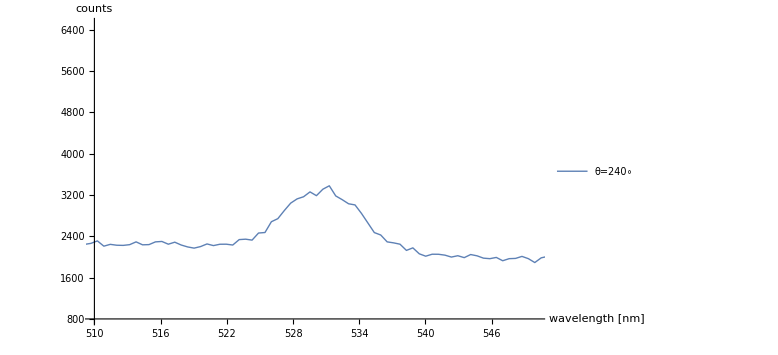

```mathematica
a240=Import["C:\\Users\\Peggy\\Desktop\\raman spectroscopz\\Raman Spectroscopy\\ramanSpectroscopy5\\analzyer angle\\SI_100_Ang_220_0240.csv","Table"];
a10=Take[a0, {200,585}];
aa240=ListLinePlot[a240, LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[0.01]] , AxesLabel->{" wavelength [nm]", " counts"}  ,PlotStyle->Directive[Thickness[Tiny],"LineColor"->Gray,AbsoluteThickness[1]],PlotLegends->LineLegend[{"θ=240∘"},LegendLayout->table], PlotRange->{{510,550}, {800,6500}}]
```

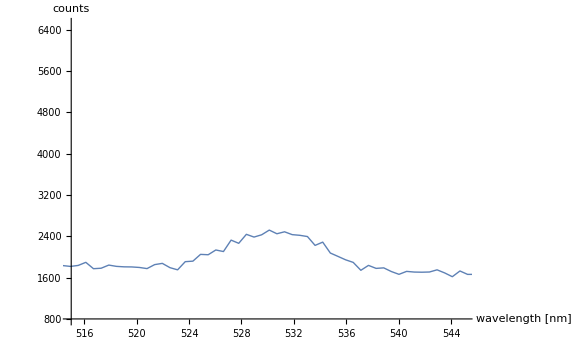

```mathematica
a250=Import["C:\\Users\\Peggy\\Desktop\\raman spectroscopz\\Raman Spectroscopy\\ramanSpectroscopy5\\analzyer angle\\SI_100_Ang_220_0250.csv","Table"];
a10=Take[a0, {200,585}];
ab=Import["C:\\Users\\Peggy\\Desktop\\raman spectroscopz\\Raman Spectroscopy\\ramanSpectroscopy5\\analzyer angle\\SI_100_Ang_220_0250.csv",{Automatic,"List",Range[1,86],{2}}]
Max[ab]
aa250=ListLinePlot[a250, LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[0.01]] , AxesLabel->{" wavelength [nm]", " counts"}  ,PlotStyle->Directive[Thickness[Tiny],"LineColor"->Cyan,AbsoluteThickness[1]],PlotLegends->LineLegend[{"θ=250∘"}, LegendLayout->table], PlotRange->{{515,545}, {800,6500}}]
```

```mathematica
|
```

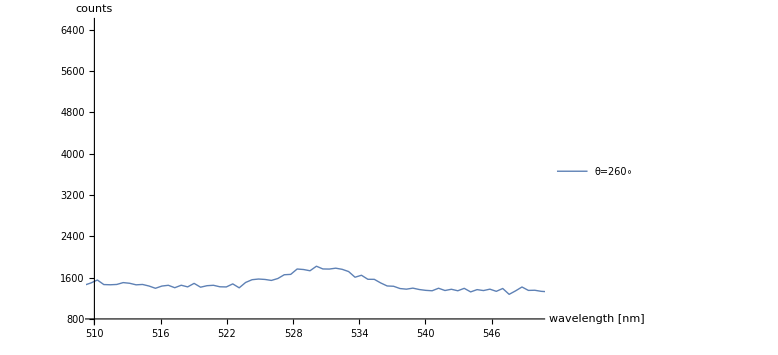

```mathematica
a260=Import["C:\\Users\\Peggy\\Desktop\\raman spectroscopz\\Raman Spectroscopy\\ramanSpectroscopy5\\analzyer angle\\SI_100_Ang_220_0260.csv","Table"];
a10=Take[a0, {200,585}];
aa260=ListLinePlot[a260, LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[0.01]] , AxesLabel->{" wavelength [nm]", " counts"}  ,PlotStyle->Directive[Thickness[Tiny],"LineColor"->Darker[Red],AbsoluteThickness[1]],PlotLegends->LineLegend[{"θ=260∘"}, LegendLayout->table], PlotRange->{{510,550}, {800,6500}}]
```

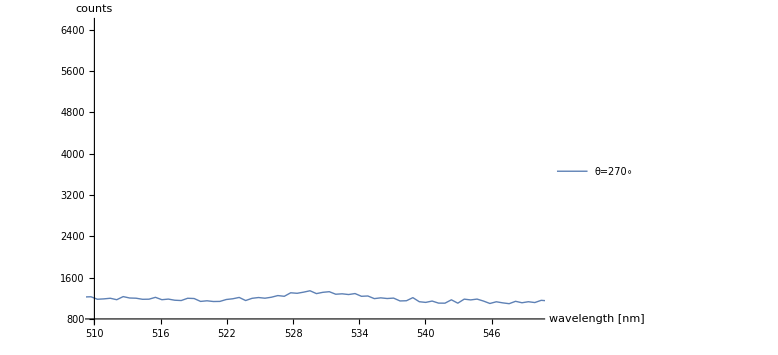

```mathematica
a270=Import["C:\\Users\\Peggy\\Desktop\\raman spectroscopz\\Raman Spectroscopy\\ramanSpectroscopy5\\analzyer angle\\SI_100_Ang_220_0270.csv","Table"];
a10=Take[a0, {200,585}];
aa270=ListLinePlot[a270, LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[0.01]] , AxesLabel->{" wavelength [nm]", " counts"}  ,PlotStyle->Directive[Thickness[Tiny],"LineColor"->Darker[Green],AbsoluteThickness[1]],PlotLegends->LineLegend[{"θ=270∘"},LegendLayout->table], PlotRange->{{510,550}, {800,6500}}]
```

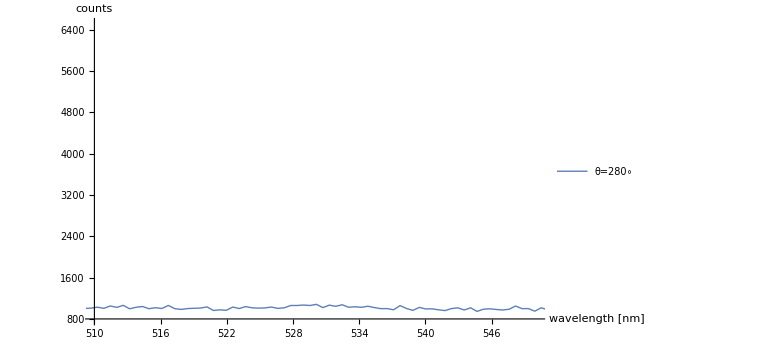

```mathematica
a280=Import["C:\\Users\\Peggy\\Desktop\\raman spectroscopz\\Raman Spectroscopy\\ramanSpectroscopy5\\analzyer angle\\SI_100_Ang_220_0280.csv","Table"];
a10=Take[a0, {200,585}];
aa280=ListLinePlot[a280, LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[0.01]] , AxesLabel->{" wavelength [nm]", " counts"}  ,PlotStyle->Directive[Thickness[Tiny],"LineColor"->Darker[Blue],AbsoluteThickness[1]],PlotLegends->LineLegend[{"θ=280∘"},LegendLayout->table], PlotRange->{{510,550}, {800,6500}}]
```

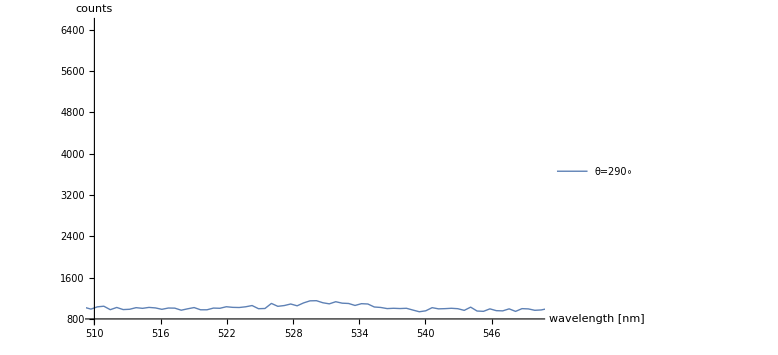

```mathematica
a290=Import["C:\\Users\\Peggy\\Desktop\\raman spectroscopz\\Raman Spectroscopy\\ramanSpectroscopy5\\analzyer angle\\SI_100_Ang_220_0290.csv","Table"];
a10=Take[a0, {200,585}];
aa290=ListLinePlot[a290, LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[0.01]] , AxesLabel->{" wavelength [nm]", " counts"}  ,PlotStyle->Directive[Thickness[Tiny],"LineColor"->Darker[Brown],AbsoluteThickness[1]],PlotLegends->LineLegend[{"θ=290∘"},LegendLayout->table], PlotRange->{{510,550}, {800,6500}}]
```

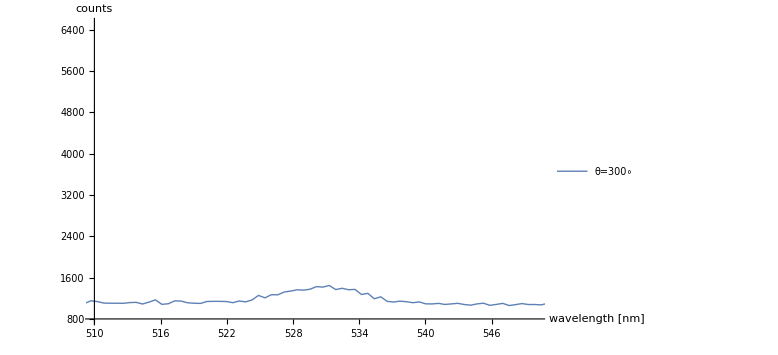

```mathematica
a300=Import["C:\\Users\\Peggy\\Desktop\\raman spectroscopz\\Raman Spectroscopy\\ramanSpectroscopy5\\analzyer angle\\SI_100_Ang_220_0300.csv","Table"];
a10=Take[a0, {200,585}];
aa300=ListLinePlot[a300, LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[0.01]] , AxesLabel->{" wavelength [nm]", " counts"}  ,PlotStyle->Directive[Thickness[Tiny],"LineColor"->Darker[Cyan],AbsoluteThickness[1]],PlotLegends->LineLegend[{"θ=300∘"},LegendLayout->table], PlotRange->{{510,550}, {800,6500}}]
```

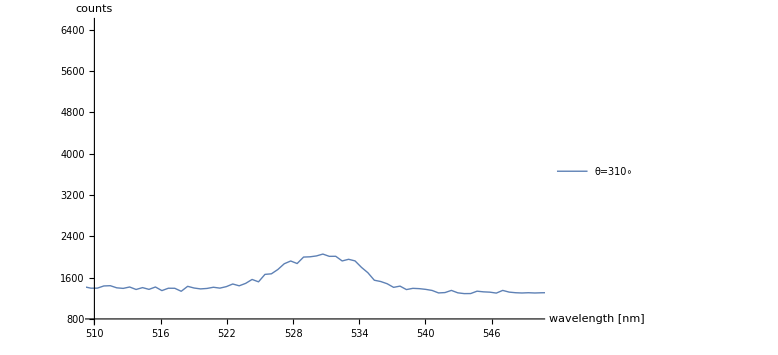

```mathematica
a310=Import["C:\\Users\\Peggy\\Desktop\\raman spectroscopz\\Raman Spectroscopy\\ramanSpectroscopy5\\analzyer angle\\SI_100_Ang_220_0310.csv","Table"];
a10=Take[a0, {200,585}];
aa310=ListLinePlot[a310, LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[0.01]] , AxesLabel->{" wavelength [nm]", " counts"}  ,PlotStyle->Directive[Thickness[Tiny],"LineColor"->Darker[Orange],AbsoluteThickness[1]],PlotLegends->LineLegend[{"θ=310∘"}, LegendLayout->table], PlotRange->{{510,550}, {800,6500}}]
```

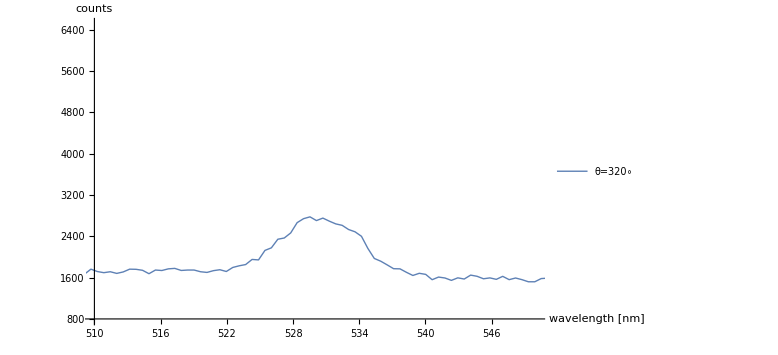

```mathematica
a320=Import["C:\\Users\\Peggy\\Desktop\\raman spectroscopz\\Raman Spectroscopy\\ramanSpectroscopy5\\analzyer angle\\SI_100_Ang_220_0320.csv","Table"];
a10=Take[a0, {200,585}];
aa320=ListLinePlot[a320, LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[0.01]] , AxesLabel->{" wavelength [nm]", " counts"}  ,PlotStyle->Directive[Thickness[Tiny],"LineColor"->Darker[Pink],AbsoluteThickness[1]],PlotLegends->LineLegend[{"θ=320∘"},LegendLayout->table], PlotRange->{{510,550}, {800,6500}}]
```

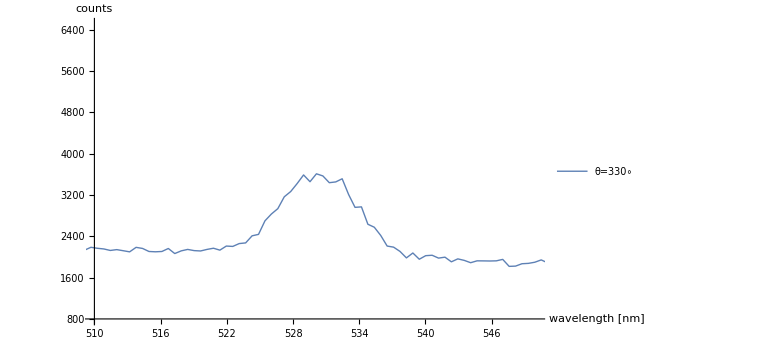

```mathematica
a330=Import["C:\\Users\\Peggy\\Desktop\\raman spectroscopz\\Raman Spectroscopy\\ramanSpectroscopy5\\analzyer angle\\SI_100_Ang_220_0330.csv","Table"];
a10=Take[a0, {200,585}];
aa330=ListLinePlot[a330, LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[0.01]] , AxesLabel->{" wavelength [nm]", " counts"}  ,PlotStyle->Directive[Thickness[Tiny],"LineColor"->Darker[Yellow]
,AbsoluteThickness[1]],PlotLegends->LineLegend[{"θ=330∘"},LegendLayout->table], PlotRange->{{510,550}, {800,6500}}]
```

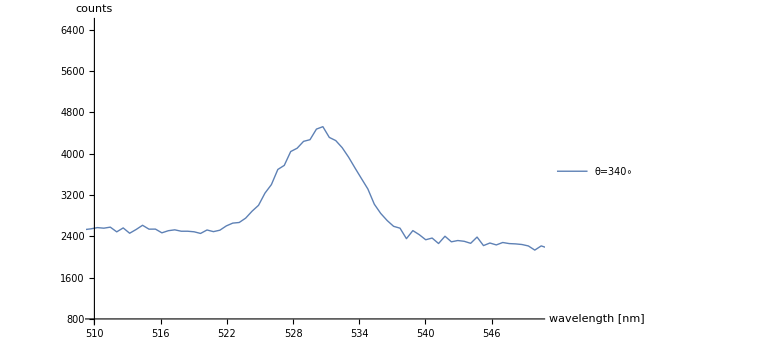

```mathematica
a340=Import["C:\\Users\\Peggy\\Desktop\\raman spectroscopz\\Raman Spectroscopy\\ramanSpectroscopy5\\analzyer angle\\SI_100_Ang_220_0340.csv","Table"];
a10=Take[a0, {200,585}];
aa340=ListLinePlot[a340, LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[0.01]] , AxesLabel->{" wavelength [nm]", " counts"}  ,PlotStyle->Directive[Thickness[Tiny],"LineColor"->Darker[Purple]
,AbsoluteThickness[1]],PlotLegends->LineLegend[{"θ=340∘"},LegendLayout->table], PlotRange->{{510,550}, {800,6500}}]
```

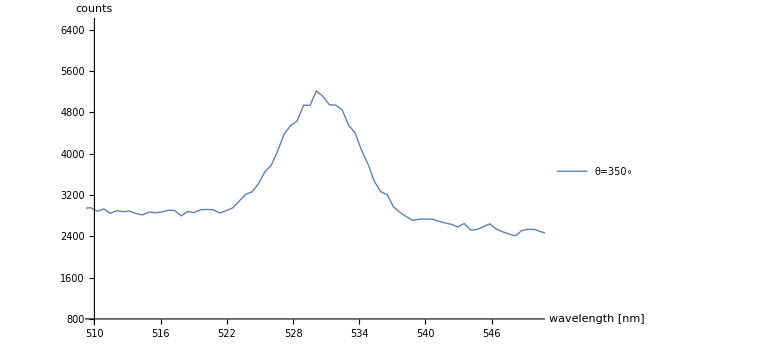

```mathematica
a350=Import["C:\\Users\\Peggy\\Desktop\\raman spectroscopz\\Raman Spectroscopy\\ramanSpectroscopy5\\analzyer angle\\SI_100_Ang_220_0350.csv","Table"];
a10=Take[a0, {200,585}];
aa350=ListLinePlot[a350, LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[0.01]] , AxesLabel->{" wavelength [nm]", " counts"}  ,PlotStyle->Directive[Thickness[Tiny],"LineColor"->Darker[Magenta],AbsoluteThickness[1]],PlotLegends->LineLegend[{"θ=350∘"},LegendLayout->table ], PlotRange->{{510,550}, {800,6500}}]
```

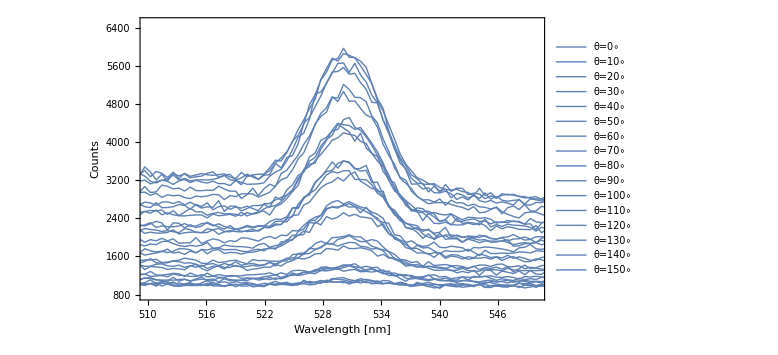

```mathematica
Show[aa0,aa10,aa20,aa30,aa40,aa50,aa60,aa70,aa80,aa90,aa100,aa110,aa120,aa130,aa140,aa150,aa160,aa230,aa240,aa250,aa260,aa270,aa280,aa290,aa300,aa310,aa320,aa330,aa340,aa350, PlotLabel->"" ,  
 LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio,FrameLabel->{"Wavelength [nm]","Counts"},Frame->True,LabelStyle->(FontFamily->"Helvetica") ]
```